```mathematica
c2=0.54;
c1=1.4;
Dc=0.76;
Fc=0.5;
fc=0.093;
```

```mathematica
gpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-e-up-xi1-pi-noD-S1.wdx"];
Hdgu=Query[1,1]@gpdu;
Heru=Query[1,2]@gpdu;
Hdau=Query[1,3]@gpdu;
Edgu=Query[2,1]@gpdu;
Eeru=Query[2,2]@gpdu;
Edau=Query[2,3]@gpdu;
Hdgf=Interpolation[Flatten[Hdgu,1]];
Herf=Interpolation[Flatten[Heru,1]];
Hdaf=Interpolation[Flatten[Hdau,1]];
dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-e-dleta-pi-xi1-S1.wdx"];
dHdgu=Query[1,1]@dgpdu;
dHeru=Query[1,2]@dgpdu;
dHdau=Query[1,3]@dgpdu;
dEdgu=Query[2,1]@dgpdu;
dEeru=Query[2,2]@dgpdu;
dEdau=Query[2,3]@dgpdu;dHdaf=Interpolation[Flatten[dHdau,1]];

Dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-e-D-xi1-pi-S1.wdx"];

DHeru=Query[1,2]@Dgpdu;
DHdau=Query[1,3]@Dgpdu;

DEeru=Query[2,2]@Dgpdu;
DEdau=Query[2,3]@Dgpdu;

DHerf=Interpolation[Flatten[DHeru,1]];
DHdaf=Interpolation[Flatten[DHdau,1]];


dDgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-e-dleta-D-pi-xi1-S1.wdx"];

dDHeru=Query[1,2]@dDgpdu;
dDHdau=Query[1,3]@dDgpdu;

dDEeru=Query[2,2]@dDgpdu;
dDEdau=Query[2,3]@dDgpdu;

dDHdaf=Interpolation[Flatten[dDHdau,1]];
```

```mathematica
(*先把上面的结果组合起来*)
```

```mathematica
Hdgall[x_,t_]:=Hdgf[x,t];
Herall[x_,t_]:=Herf[x,t]+Hdaf[x,t]+dHdaf[x,t]+DHerf[x,t]+DHdaf[x,t]+dDHdaf[x,t];
```

```mathematica
(*u quark*)
```

```mathematica
(*Σ0 k+,只需要乘上系数，u=sbar=pi+的结果*)
Coep1=(-I)*(Dc-Fc)^2/(4*(0.093)^2*2*(2Pi)^4);
(*k+的u贡献，分段但就是总的*)
k1Hdg[x_,t_]=Coep1*Hdgall[x,t];
k1Her[x_,t_]=Coep1*Herall[x,t];
(*k0没有u夸克*)
(*图的u夸克总结果，就是对粒子求和*)
Hdgzall[x_,t_]=k1Hdg[x,-t];
Herallwhole[x_,t_]=k1Her[x,-t];
```

```mathematica
(*d quark*)
(*k0的d夸克，与pi0不同输入没有1/2*)
ap0=(-I)*(Dc-Fc)^2/(2*2*(0.093)^2*(2Pi)^4);
(*k0的d夸克，直接就是结果没有反转*)
k0Hdg[x_,t_]=ap0*Hdgall[x,t];
k0Her[x_,t_]=ap0*Herall[x,t];
(*图的d夸克总结果，就是对粒子求和*)
Hdgzalld[x_,t_]=k0Hdg[x,-t];
Herallwholed[x_,t_]=k0Her[x,-t];
```

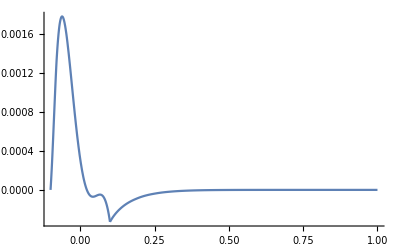

```mathematica
Show[Plot[Hdgzall[x,1],{x,0.1,1},PlotRange->All],Plot[Herallwhole[x,1],{x,-0.1,0.1},PlotRange->All]]
```

```mathematica
(*s quark*)
```

```mathematica
(*k+,sbar=u，所以之后再对dbar反转得到d*)
(*pi+的dbar贡献就是u，反转*)
k1Hdgs[x_,t_]=-k1Hdg[-x,t];
k1Hers[x_,t_]=-k1Her[-x,t];


(*k0,sbar=d*)
k0Hdgs[x_,t_]=-k0Hdg[-x,t];
k0Hers[x_,t_]=-k0Her[-x,t];
(*图的总结果，就是对粒子求和*)
Hdgfalls[x_,t_]=k1Hdgs[x,-t]+k0Hdgs[x,-t];
Herallwholes[x_,t_]=k1Hers[x,-t]+k0Hers[x,-t];
```

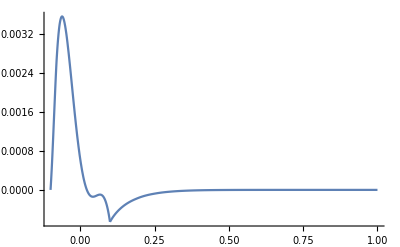

```mathematica
Show[Plot[Hdgzalld[x,1],{x,0.1,1},PlotRange->All],Plot[Herallwholed[x,1],{x,-0.1,0.1},PlotRange->All]]
```

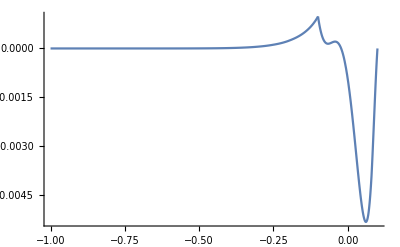

```mathematica
Show[Plot[Hdgfalls[x,1],{x,-1,-0.1},PlotRange->All],Plot[Herallwholes[x,1],{x,-0.1,0.1},PlotRange->All]]
```

```mathematica
pathu=FileNameJoin[{"G:\\calc-online\\gpd\\drawpic\\baryon\\gpd\\result",
"u-diagram-e-S.wdx"}];
pathd=FileNameJoin[{"G:\\calc-online\\gpd\\drawpic\\baryon\\gpd\\result",
"d-diagram-e-S.wdx"}];
paths=FileNameJoin[{"G:\\calc-online\\gpd\\drawpic\\baryon\\gpd\\result",
"s-diagram-e-S.wdx"}];
outu=<|"H"-><|"DGz"->Hdgzall[x,t],"ER"->Herallwhole[x,t],"DGf"->0|>|>;
outd=<|"H"-><|"DGz"->Hdgzalld[x,t],"ER"->Herallwholed[x,t],"DGf"->0|>|>;
outs=<|"H"-><|"DGz"->0,"ER"->Herallwholes[x,t],"DGf"->Hdgfalls[x,t]|>|>;
Export[pathu,outu]
Export[pathd,outd]
Export[paths,outs]
```

G:\calc-online\gpd\drawpic\baryon\gpd\result\u-diagram-e-S.wdx

G:\calc-online\gpd\drawpic\baryon\gpd\result\d-diagram-e-S.wdx

G:\calc-online\gpd\drawpic\baryon\gpd\result\s-diagram-e-S.wdx